The idea is to make a two point vector Pade approximation.  
	f⃗(x)≈(p⃗(x))/(q(x))
In practice the dimension is large.  I am going to experiment to see if I can use an averaged scalar data set to construct 
	q(x)=1+q_1 x+…+q_n x^n
and then subsequently compute each component of p⃗(x) as just the two point “Hermite” fit to f⃗(x)q(x)≈p(x).

Each component "i" would generate a different denominator.   I am going to use an SVD to compute the strongest signal individual component.

I am going to think of this as generating a polynomial centered on the midpoint z=(a+b)/2 and defined by the two sets of data f^(0:r)(+Δ) and f^(0:r)(-Δ) from the end points where Δ=(b-a)/2.

## Scalar Denominator

For a scalar complex function f(z) I want to generate a maximally consistent polynomial approximation to the reciprocal q(z)≈1/f(z) using the two point data f^(0:r)(±Δ).  I have 2(r+1) data points so generically I should be able to determine 2(r+1) coefficients q_0+q_1 z+q_2 z^2+…+q_(2r+1)z^(2r+1).  I can think of computing the reciprocal of of either the infinite coefficients of f or the finite coefficients of q.

The first things to do is compute the list of derivatives of 1/f from the list of derivatives of f.

```mathematica
Clear[f,x]
hmm=1/f[x];
Simplify[Join[{1/f[x]},Table[
hmm=D[hmm,x],
{6}]]/.{
f[x]->fDers⟦1⟧,
Derivative[n_][f][x]:>fDers⟦n+1⟧}]
```

Part::partd: Part specification fDers⟦1⟧ is longer than depth of object.

Part::partd: Part specification fDers⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{1/fDers⟦1⟧,-fDers⟦2⟧/fDers⟦1⟧^2,(2 fDers⟦2⟧^2-fDers⟦1⟧ fDers⟦3⟧)/fDers⟦1⟧^3,-(6 fDers⟦2⟧^3-6 fDers⟦1⟧ fDers⟦2⟧ fDers⟦3⟧+fDers⟦1⟧^2 fDers⟦4⟧)/fDers⟦1⟧^4,1/fDers⟦1⟧^5(24 fDers⟦2⟧^4-36 fDers⟦1⟧ fDers⟦2⟧^2 fDers⟦3⟧+6 fDers⟦1⟧^2 fDers⟦3⟧^2+8 fDers⟦1⟧^2 fDers⟦2⟧ fDers⟦4⟧-fDers⟦1⟧^3 fDers⟦5⟧),1/fDers⟦1⟧^6(-120 fDers⟦2⟧^5+240 fDers⟦1⟧ fDers⟦2⟧^3 fDers⟦3⟧-60 fDers⟦1⟧^2 fDers⟦2⟧^2 fDers⟦4⟧+10 fDers⟦1⟧^2 fDers⟦2⟧ (-9 fDers⟦3⟧^2+fDers⟦1⟧ fDers⟦5⟧)+fDers⟦1⟧^3 (20 fDers⟦3⟧ fDers⟦4⟧-fDers⟦1⟧ fDers⟦6⟧)),1/fDers⟦1⟧^7(720 fDers⟦2⟧^6-1800 fDers⟦1⟧ fDers⟦2⟧^4 fDers⟦3⟧+480 fDers⟦1⟧^2 fDers⟦2⟧^3 fDers⟦4⟧-90 fDers⟦1⟧^2 fDers⟦2⟧^2 (-12 fDers⟦3⟧^2+fDers⟦1⟧ fDers⟦5⟧)+12 fDers⟦1⟧^3 fDers⟦2⟧ (-30 fDers⟦3⟧ fDers⟦4⟧+fDers⟦1⟧ fDers⟦6⟧)+fDers⟦1⟧^3 (-90 fDers⟦3⟧^3+30 fDers⟦1⟧ fDers⟦3⟧ fDers⟦5⟧+fDers⟦1⟧ (20 fDers⟦4⟧^2-fDers⟦1⟧ fDers⟦7⟧)))}

```mathematica
T
Derivative[i][1/f[x]]]
```

#### Code

```mathematica
Clear[RecipDers1]
RecipDers1[fDers_List]:= Module[{r=Length[fDers]-1,rDers},
(* Max Order is 7 *) 
rDers={1/fDers⟦1⟧};
If[r>1, rDers=Join[rDers,{-fDers⟦2⟧/fDers⟦1⟧^2}]];
If[r>2, rDers=Join[rDers,{(2 fDers⟦2⟧^2-fDers⟦1⟧ fDers⟦3⟧)/fDers⟦1⟧^3}]];
If[r>3, rDers=Join[rDers,{-(6 fDers⟦2⟧^3-6 fDers⟦1⟧ fDers⟦2⟧ fDers⟦3⟧+fDers⟦1⟧^2 fDers⟦4⟧)/fDers⟦1⟧^4}]];
If[r>4, rDers=Join[rDers,
{1/fDers⟦1⟧^5(24 fDers⟦2⟧^4-36 fDers⟦1⟧ fDers⟦2⟧^2 fDers⟦3⟧+6 fDers⟦1⟧^2 fDers⟦3⟧^2+8 fDers⟦1⟧^2 fDers⟦2⟧ fDers⟦4⟧-fDers⟦1⟧^3 fDers⟦5⟧)}]];
If[r>5, rDers=Join[rDers,
{1/fDers⟦1⟧^6(-120 fDers⟦2⟧^5+240 fDers⟦1⟧ fDers⟦2⟧^3 fDers⟦3⟧-60 fDers⟦1⟧^2 fDers⟦2⟧^2 fDers⟦4⟧+10 fDers⟦1⟧^2 fDers⟦2⟧ (-9 fDers⟦3⟧^2+fDers⟦1⟧ fDers⟦5⟧)+fDers⟦1⟧^3 (20 fDers⟦3⟧ fDers⟦4⟧-fDers⟦1⟧ fDers⟦6⟧))}]];
If[r>6, rDers=Join[rDers,
{1/fDers⟦1⟧^7(720 fDers⟦2⟧^6-1800 fDers⟦1⟧ fDers⟦2⟧^4 fDers⟦3⟧+480 fDers⟦1⟧^2 fDers⟦2⟧^3 fDers⟦4⟧-90 fDers⟦1⟧^2 fDers⟦2⟧^2 (-12 fDers⟦3⟧^2+fDers⟦1⟧ fDers⟦5⟧)+12 fDers⟦1⟧^3 fDers⟦2⟧ (-30 fDers⟦3⟧ fDers⟦4⟧+fDers⟦1⟧ fDers⟦6⟧)+fDers⟦1⟧^3 (-90 fDers⟦3⟧^3+30 fDers⟦1⟧ fDers⟦3⟧ fDers⟦5⟧+fDers⟦1⟧ (20 fDers⟦4⟧^2-fDers⟦1⟧ fDers⟦7⟧)))}]];
rDers]
f[x_]:= Sin[x Cos[x^2]+x]+Cos[x]
g[x_]:=1/f[x]
fDers=Table[Derivative[i][f][0],{i,0, 8}]
gDers=Table[Derivative[i][g][0],{i,0, 7}]
RecipDers1[fDers]
```

{1,2,-1,-8,1,-28,-1,4912,1}

{1,-2,9,-52,405,-3812,43029,-566872}

{1,-2,9,-52,405,-3812,43029}

```mathematica
Clear[DenominatorFit]
DenominatorFit[fDers_List,Δ_Complex]:= Module[
{r=Length[fDers]-1,RDersPlus=fDers⟦All,1⟧, RDersMinus=fDers⟦All,2⟧},
{r,Δ,RDersPlus, RDersMinus}]
DenominatorFit[{{1.0,0.2}},0.1+0.0 I]
```

{0,0.1+0. ⅈ,{1.},{0.2}}

#### Hermite Approximation

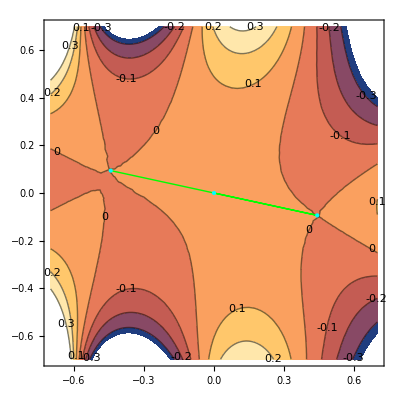

```mathematica
r=1;
ϵ=0.7;
Δ=ϵ RandomComplex[{-1-I,1+I}];
f[z_]:=Sin[Cos[z]+z+1.2 z^2]/(1+z^2)
q[z_]:= Sum[qq[i] z^i,{i,0, 2r+1}]
qFit[z_]=q[z]/.Solve[
Flatten[Table[
Derivative[i][f][z]==Derivative[i][q][z],
{i,0,r},{z,{-Δ,Δ}}]]]⟦1⟧;
ContourPlot[Re[f[x+I y]- qFit[x+ I y]]/Abs[f[x+I y]],{x,-ϵ,ϵ},{y,-ϵ,ϵ},ContourLabels->True,
Epilog->{{Green,Line[ReIm[ {0,Δ,-Δ}]]},{Cyan,Point[ReIm[ {0,Δ,-Δ}]]}}]
```

1/((2.32441-0.136738 ⅈ)-(3.62257-1.46506 ⅈ) z+(20.6755+1.55093 ⅈ) z^2-(39.1769-7.1841 ⅈ) z^3+(32.6319+4.38139 ⅈ) z^4-(24.6393-7.7033 ⅈ) z^5)

1/((2.32441-0.136738 ⅈ)-(3.62257-1.46506 ⅈ) z+(20.6755+1.55093 ⅈ) z^2-(39.1769-7.1841 ⅈ) z^3+(32.6319+4.38139 ⅈ) z^4-(24.6393-7.7033 ⅈ) z^5)

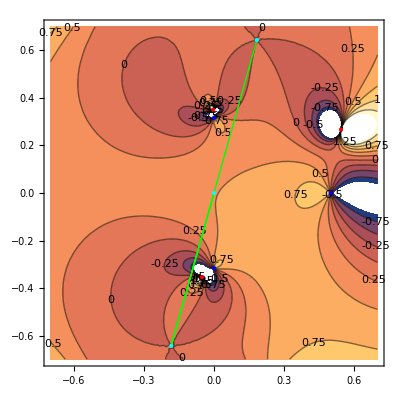

```mathematica
r=2;
ϵ=0.7;
Δ=ϵ RandomComplex[{-1-I,1+I}];
f[z_]:=Sin[Cos[z]+z+1.2 z^2]/((1+10 z^2)(1-2 z))
fRecip[z_]:=1/f[z]
q[z_]:= Sum[qq[i] z^i,{i,0, 2r+1}]
qRecip[z_]:=1/q[z]
Quiet[qRecipFit1[z_]=qRecip[z]/.Solve[
Flatten[Table[
Derivative[i][f][z]==Derivative[i][qRecip][z],
{i,0,r},{z,{-Δ,Δ}}]]]⟦1⟧]
qRecipFit2[z_]=qRecip[z]/.Solve[
Flatten[Table[
Derivative[i][fRecip][z]==Derivative[i][q][z],
{i,0,r},{z,{-Δ,Δ}}]]]⟦1⟧
ContourPlot[Re[f[x+I y]- qRecipFit1[x+ I y]]/Abs[f[x+I y]],{x,-ϵ,ϵ},{y,-ϵ,ϵ},ContourLabels->True,
Epilog->{
{Red,Point[ ReIm[z/.NSolve[1/qRecipFit1[z]==0,z]]]},
{Blue,Point[ReIm[z/.NSolve[Denominator[f[z]]==0,z]]]},
{Green,Line[ReIm[ {0,Δ,-Δ}]]},{Cyan,Point[ReIm[ {0,Δ,-Δ}]]}}]
```

```mathematica
z/.NSolve[1/qRecipFit1[z]==0,z]
z/.NSolve[Denominator[f[z]]==0,z]
```

{-0.0520073-0.353737 ⅈ,-0.00339266+0.350813 ⅈ,0.246947-0.910502 ⅈ,0.420338+1.18552 ⅈ,0.54393+0.267084 ⅈ}

{0.-0.316228 ⅈ,0.+0.316228 ⅈ,0.5}

I get a linear system by taking the reciprocal.  All I really need is the power series of the reciprocal of a a power series. I get this from the series for 1/(1-y)=∑_(i=0)^∞ y^i.  If I substitute y=∑_(j=1)^d b_j x^j then I get 
	1/(1-∑_(j=1)^d b_j x^j)=∑_(i=1)^∞ (∑_(j=1)^d b_j x^j)^i

```mathematica
p=4;
Series[Sum[(Sum[b[j] x^j,{j,1,p}])^i,{i,1,p+1}],{x,0,p}]
CoefficientList[Sum[(Sum[b[j] x^j,{j,1,p}])^i,{i,1,p+1}],x,p+1]
Clear[d]
d[0]=1;
d[1]=b[1];
d[n_]:=d[n]=Expand[Sum[d[k]*b[n-k],{k,0,n-1}]]
Join[{0},Table[d[i],{i,1,p}]]
```

b[1] x+(b[1]^2+b[2]) x^2+(b[1]^3+2 b[1] b[2]+b[3]) x^3+(b[1]^4+3 b[1]^2 b[2]+b[2]^2+2 b[1] b[3]+b[4]) x^4+O[x]^5

{0,b[1],b[1]^2+b[2],b[1]^3+2 b[1] b[2]+b[3],b[1]^4+3 b[1]^2 b[2]+b[2]^2+2 b[1] b[3]+b[4]}

{0,b[1],b[1]^2+b[2],b[1]^3+2 b[1] b[2]+b[3],b[1]^4+3 b[1]^2 b[2]+b[2]^2+2 b[1] b[3]+b[4]}

```mathematica
Series[1/(1-y),{y,0,12}]
```

1+y+y^2+y^3+y^4+y^5+y^6+y^7+y^8+y^9+y^10+y^11+y^12+O[y]^13

```mathematica
Clear[f,g,x]
f[x_]:= 1/g[x]
f'[x]
Together[f''[x]]
Together[f'''[x]]
```

-g'[x]/g[x]^2

(2 g'[x]^2-g[x] g''[x])/g[x]^3

(-6 g'[x]^3+6 g[x] g'[x] g''[x]-g[x]^2 g^(3)[x])/g[x]^4

```mathematica
Clear[f,q]
TableForm[
ListConvolve[Table[q[i],{i,0,3}], Table[f[i],{i,0,12}] ],
TableHeadings->{Range[0,12],None}
]
```

0 | f[3] q[0]+f[2] q[1]+f[1] q[2]+f[0] q[3]
1 | f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
2 | f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
3 | f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3]
4 | f[7] q[0]+f[6] q[1]+f[5] q[2]+f[4] q[3]
5 | f[8] q[0]+f[7] q[1]+f[6] q[2]+f[5] q[3]
6 | f[9] q[0]+f[8] q[1]+f[7] q[2]+f[6] q[3]
7 | f[10] q[0]+f[9] q[1]+f[8] q[2]+f[7] q[3]
8 | f[11] q[0]+f[10] q[1]+f[9] q[2]+f[8] q[3]
9 | f[12] q[0]+f[11] q[1]+f[10] q[2]+f[9] q[3]

## Scalar Pade Approximation

The scalar problem to approximate  f(x)≈p(x)/q(x) with p(x) of degree m and q(x) of degree n with q(0)=1 is standard. All I do is clear the fraction and match coefficients.  It looks like this
	q(x)f(x)-p(x)=0+0 x+…+0 x^m+0 x^(m+1)+…+0 x^(m+n)+O(x^(n+m+1))
The m+1 coefficients in the numerator p(x) are directly determined by the first  m+1 equations.  The n unknown coefficients in the denominator q(x) are determined by the next n equations.  The coefficients of q(x)*f(x) are the convolution of the coefficients of q(x) and a sufficiently long truncation of the power series for f.  Some parts of the literature tends to use any element of the null space of the n×(m+1) Toeplitz matrix
	T=(f[m+1] | f[m] | … | f[1]
f[m+2] | f[m+1] |   | f[2]
⋮ |   |   |  
f[m+n] |   |   |  )
as the coefficients of the denominator.  I am making the decision that I am using raw polynomials. I will add i! scalings to and from the power series representations if (and when) needed.  I am hedging on the decision to use the solution q(x)=1+q_1 x+… 	For now I am going to hold onto q_0 in the derivation.

```mathematica
Clear[m,n,f,fs,p,ps,q,qs]
{m,n}={7,3};
{fs,ps,qs}={
Array[f,m+n+1,0],
Array[p,m+1,0],
Array[q,n+1,0]};
CoeffToPoly[coeffs_List,x_]:=Sum[coeffs⟦i⟧x^(i-1),{i,Length[coeffs]}]
Eqs=CoefficientList[CoeffToPoly[fs,x]CoeffToPoly[qs,x]-CoeffToPoly[ps,x],x]⟦1;;m+n+1⟧;
TableForm[Eqs⟦1;;m+1⟧,TableHeadings->{Table[x^i,{i,0,m}],Automatic}]
TableForm[Eqs⟦m+2;;m+n+1⟧,TableHeadings->{Table[x^i,{i,m+1,m+n}],Automatic}]
```

1 | -p[0]+f[0] q[0]
x | -p[1]+f[1] q[0]+f[0] q[1]
x^2 | -p[2]+f[2] q[0]+f[1] q[1]+f[0] q[2]
x^3 | -p[3]+f[3] q[0]+f[2] q[1]+f[1] q[2]+f[0] q[3]
x^4 | -p[4]+f[4] q[0]+f[3] q[1]+f[2] q[2]+f[1] q[3]
x^5 | -p[5]+f[5] q[0]+f[4] q[1]+f[3] q[2]+f[2] q[3]
x^6 | -p[6]+f[6] q[0]+f[5] q[1]+f[4] q[2]+f[3] q[3]
x^7 | -p[7]+f[7] q[0]+f[6] q[1]+f[5] q[2]+f[4] q[3]

x^8 | f[8] q[0]+f[7] q[1]+f[6] q[2]+f[5] q[3]
x^9 | f[9] q[0]+f[8] q[1]+f[7] q[2]+f[6] q[3]
x^10 | f[10] q[0]+f[9] q[1]+f[8] q[2]+f[7] q[3]

```mathematica
MatrixForm[
CoefficientArrays[
Eqs⟦m+2;;m+n+1⟧,
qs]⟦2⟧]
```

(f[8] | f[7] | f[6] | f[5]
f[9] | f[8] | f[7] | f[6]
f[10] | f[9] | f[8] | f[7])

The terms x^(m+1) up to x^(m+n) are determined by the Toeplitz matrix

```mathematica
Clear[f]
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T]
```

(f[8] | f[7] | f[6] | f[5]
f[9] | f[8] | f[7] | f[6]
f[10] | f[9] | f[8] | f[7])

OK.  I should be able to test this against the built in Pade Approximants.  For a

The process breaks for some functions and orders.

```mathematica
Clear[f,fun,x]
fun[x_]:=Cos[x]
pMax=21;
Table[
f[i]=Coefficient[Normal[Series[fun[x],{x,0,pMax+1}]],x,i],
{i,0,pMax,1}];
{m,n}={7,7};
pad[x_]=PadeApproximant[fun[x],{x,0, {m,n}}];
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T];
{v1}=NullSpace[T]
v1=v1/v1⟦1⟧
CoefficientList[Denominator[pad[x]],x]
```

{{0,39251520/127,0,1154160/127,0,16632/127,0,1}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity,Indeterminate,ComplexInfinity}

{1,0,229/7788,0,1/2360,0,127/39251520}

```mathematica
{m,n}
pad[x]
```

{7,7}

(1-(3665 x^2)/7788+(711 x^4)/25960-(2923 x^6)/7850304)/(1+(229 x^2)/7788+x^4/2360+(127 x^6)/39251520)

0.841471/(1.-0.89893 x+1.73671 x^2-1.99715 x^3+2.95729 x^4-3.79095 x^5+5.24135 x^6)

1.1884-1.06828 x+2.06389 x^2-2.37341 x^3+3.51443 x^4-4.50514 x^5+6.2288 x^6

1.1884-1.06828 x+2.06389 x^2-2.37341 x^3+3.51443 x^4-4.50514 x^5+6.2288 x^6

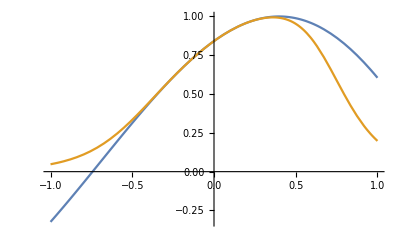

```mathematica
f[x_]:=Sin[Exp[0.4 x]+x]
p[x_]=N[PadeApproximant[f[x],{x,0,{0,6}}]]
Simplify[1/p[x]]
Expand[N[Normal[Series[1/f[x],{x,0, 6}]]]]
Plot[{f[x],p[x]},{x, -1,1}]
```

```mathematica
Clear[f,fun,x]
fun[x_]:=Exp[x]/((1-x)^2+1/1000)
pMax=21;
Table[
f[i]=Coefficient[Normal[Series[fun[x],{x,0,pMax+1}]],x,i],
{i,0,pMax,1}];
{m,n}={5,5};
pad[x_]=PadeApproximant[fun[x],{x,0, {m,n}}];
T=ToeplitzMatrix[Table[f[i],{i,m+1,m+n,1}],Table[f[i],{i, m+1,1+m-n,-1}]];
T=T/.f[i_]:>If[i≥0,f[i],0];
MatrixForm[T];
{v1}=NullSpace[T];
v1=v1/v1⟦1⟧
CoefficientList[Denominator[pad[x]],x]
```

{1,-232408464109788754660721143/97619723002948778075730286,799493989077988243167863143/439288753513269501340786287,-1750066436406072854559291143/3514310028106156010726290296,3084125806094042588835005143/49200340393486184150168064144,-4801672098141897445995005143/1476010211804585524505041924320}

{1,-232408464109788754660721143/97619723002948778075730286,799493989077988243167863143/439288753513269501340786287,-1750066436406072854559291143/3514310028106156010726290296,3084125806094042588835005143/49200340393486184150168064144,-4801672098141897445995005143/1476010211804585524505041924320}

```mathematica
NullSpace[T]
```

{{-3165565566240/9376239571,1186285428720/9376239571,-3334807267680/9376239571,1195661794740/9376239571,-169241787990/9376239571,1}}

```mathematica
fun[x]
pad[x]
```

ⅇ^x/(1/1000+(1-x)^2)

(1000/1001+(30097732516210432719071500 x)/48809861501474389037865143+(76133425597104440868143000 x^2)/439288753513269501340786287+(86843993571545518760625125 x^3)/3075021274592886509385504009+(16811489763960091608767875 x^4)/6150042549185773018771008018+(4793586529498564036053575 x^5)/36900255295114638112626048108)/(1-(232408464109788754660721143 x)/97619723002948778075730286+(799493989077988243167863143 x^2)/439288753513269501340786287-(1750066436406072854559291143 x^3)/3514310028106156010726290296+(3084125806094042588835005143 x^4)/49200340393486184150168064144-(4801672098141897445995005143 x^5)/1476010211804585524505041924320)

```mathematica
den[x_]=Denominator[pad[x]]
```

1-(232408464109788754660721143 x)/97619723002948778075730286+(799493989077988243167863143 x^2)/439288753513269501340786287-(1750066436406072854559291143 x^3)/3514310028106156010726290296+(3084125806094042588835005143 x^4)/49200340393486184150168064144-(4801672098141897445995005143 x^5)/1476010211804585524505041924320

```mathematica
den[0.1]
```

0.779633

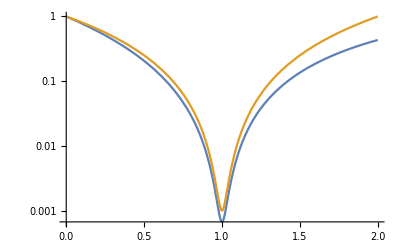

```mathematica
LogPlot[{den[x],1/1000+(1-x)^2},{x,0, 2}]
```

```mathematica
Solve[Denominator[pad[x]]==0,x]//N
```

{{x→6.40205},{x→1.-0.0316222 ⅈ},{x→1.+0.0316222 ⅈ},{x→5.43351-4.29465 ⅈ},{x→5.43351+4.29465 ⅈ}}

{5,5}

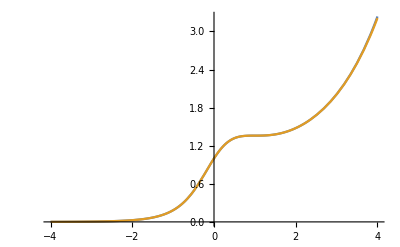

```mathematica
{m,n}
Plot[{pad[x],fun[x]},{x,-4,4}]
```

```mathematica
Dimensions[T]
SingularValueList[N[T]]
NullSpace[T]
```

{7,8}

{0.503462,0.503462,0.00207295,0.00207295,3.86712×10^-7,3.86545×10^-7,1.33825×10^-11}

{{0,39251520/127,0,1154160/127,0,16632/127,0,1}}

```mathematica
PadeApproximant[fun[x],{x,0, {m,n}}]
```

(1-(3665 x^2)/7788+(711 x^4)/25960-(2923 x^6)/7850304)/(1+(229 x^2)/7788+x^4/2360+(127 x^6)/39251520)

## Integration of Pade Rational Approximations.

Integrating the approximation ∫_a^b p(z)/q(z)dx over is simple.  The break down into simple rational expressions is very fast and ∫_a^b 1/(z-c)dz=ln(c-a)-ln(c-b)+C with a possible C=±2π ⅈ depending on wether the integration path crosses the branch cut along the negative real axis or not. Because of the minus signs in the recipe and the shifts the transformed branch cut is along the horizontal ray from c to c+∞.  C=0  if it does not cross. C=±2π ⅈ is if does with the sign determined by the direction.

```mathematica
{dp,dq}={10,12};
p[z_]=Sum[RandomComplex[] z^i,{i,0,dp}];
q[z_]=Sum[RandomComplex[] z^i,{i,0,dq}];
Timing[Hmm=Chop[Apart[ p[z]/q[z]]]/.{1.0->1}]
```

{0.,-(0.0237561+0.168421 ⅈ)/((-0.946625-0.442895 ⅈ)+z)-(0.0357558-0.0783699 ⅈ)/((-0.887538+0.444972 ⅈ)+z)-(0.0794508-0.159383 ⅈ)/((-0.517464+0.712662 ⅈ)+z)+(0.0286383-0.0946658 ⅈ)/((-0.435776-0.944339 ⅈ)+z)-(0.113409-0.0697184 ⅈ)/((-0.189282-0.619483 ⅈ)+z)-(0.225385-0.210419 ⅈ)/((0.0441491+1.06142 ⅈ)+z)+(0.610069+0.15247 ⅈ)/((0.140684+0.659879 ⅈ)+z)+(0.00136555-0.0798524 ⅈ)/((0.286184-1.02247 ⅈ)+z)-(0.216158+0.0430576 ⅈ)/((0.662184+0.811688 ⅈ)+z)+(0.117394-0.196873 ⅈ)/((0.670588+0.214727 ⅈ)+z)-(0.0927517-0.0934763 ⅈ)/((0.707442-0.701057 ⅈ)+z)+(0.0291988-0.180966 ⅈ)/((1.07148-0.157551 ⅈ)+z)}

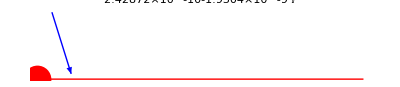

```mathematica
Clear[a,b,c,z,f1]
{a,b,c}=RandomComplex[{-1-I,1+I},3];
f1[z_]=1/(z-c);
Timing[I1=Integrate[ f1[(1-t)a+t b] (a-b) ,{t,0,1}]];
Timing[I2=NIntegrate[ f1[(1-t)a+t b] (a-b) ,{t,0,1}]];
Timing[I3=Log[ c-a]-Log[c-b]];
Graphics[{
{Blue, Arrow[ReIm[{a,b}]]},
{Red, PointSize[0.05],Point[ReIm[c]],Line[ReIm[{c,c+3}]]}
},
PlotLabel->I1-I3
]
```

Any numerical difficulty in the integration is resolved analytically!